```mathematica
SetDirectory["/Users/navonilsaha/Documents/Clousure_Relationships-Radio_Afterglow"]
sigdata=Import["CR_Radio (2).tsv", "Table",HeaderLines -> 1];
```

/Users/navonilsaha/Documents/Clousure_Relationships-Radio_Afterglow

```mathematica
fullabplot={};
Do[
alpha=sigdata[[i,2]];
beta=sigdata[[i,4]] ;
aErr = sigdata[[i,3]];
bErr = sigdata[[i,5]];
If[alpha*beta!=0.0,
AppendTo[fullabplot,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}]];
,{i,1,Length[sigdata]}];
```

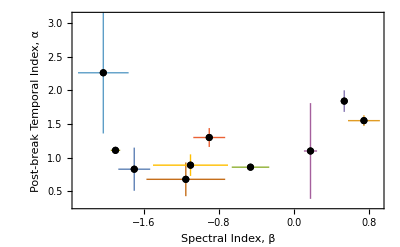

```mathematica
fullrelation=ListPlot[fullabplot,PlotStyle->Black];
Show[fullrelation,PlotRange->{{-2.30,.90},{0.3,3.10}},AxesOrigin->{1,0},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->18},Frame->True,FrameLabel->{{"Post-break Temporal Index, α",""},{"Spectral Index, β","Full Sample N=10"}},LabelStyle->Directive[Black]]
```

```mathematica
Clear[FastIII]
Clear[SlowIII]
Clear[plotFastIII]
Clear[plotSlowIII]
Clear[plotFastIIIErr]
Clear[plotSlowIIIErr]
FastIII={};
SlowIII={};
plotFastIII={};
plotSlowIII={};
plotFastIIIErr={};
plotSlowIIIErr={};
```

```mathematica
Do[
alpha=sigdata[[i,2]];
beta=sigdata[[i,4]] ;
aErr = sigdata[[i,3]];
bErr = sigdata[[i,5]];
If[alpha*beta*aErr*bErr!=0.0,
AppendTo[total,i];
rectCheck=Rectangle[{beta-bErr,alpha-aErr},{beta+bErr,alpha+aErr}];

r1=ImplicitRegion[x+(2/3)==y,{{x,0.5,2},y}];
r2=ImplicitRegion[(3*x+2)/2==y,{{x,3,5},y}];
regUni=RegionUnion[r1,r2];
regInt=RegionIntersection[rectCheck,regUni];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[SlowIII,i];
AppendTo[plotSlowIII,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotSlowIIIErr,{Graphics[{EdgeForm[Directive[Dashed,Orange]],FaceForm[],Rectangle[{beta-bErr,alpha-aErr},{beta+bErr,alpha+aErr}]}]}];
];

],{i,1,Length[sigdata]}];
```

AppendTo::rvalue: total is not a variable with a value, so its value cannot be changed.

General::stop: Further output of AppendTo::rvalue will be suppressed during this calculation.

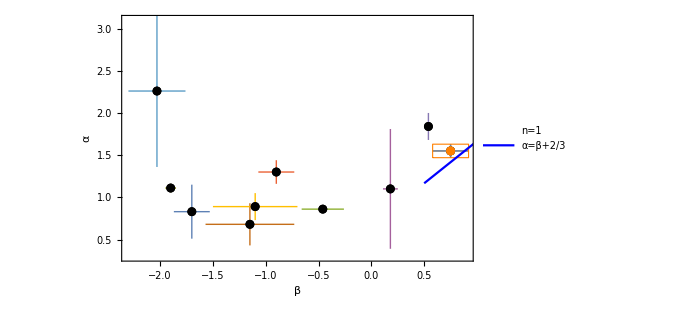

```mathematica
reg0 = With[{t=.0004,d=.5,background=White},Plot[{0*x},{x,.5,2},PlotRange->{{-2.0,2.0},{-2.0,2.0}},PlotStyle->{White},PlotLegends->Placed[{"n="<>ToString[Length[SlowIII]]},{0.9,0.878}]]];
reg1=With[{t=.0004,d=.5,background=White},Plot[{x+(2/3)},{x,0.5,1},PlotRange->{{-2.0,2.0},{-2.0,2.0}},PlotStyle->{Blue},PlotLegends->Placed[{"α=β+2/3"},{0.78,0.878}]]];
reg2=With[{t=.0004,d=.5,background=White},Plot[{(3*x+2)/2},{x,0.5,2},PlotRange->{{-2.0,3.0},{-2.0,3.0}},PlotStyle->{Purple},PlotLegends->Placed[{"α=(3β+2)/2"},{0.75,0.878}]]];
baseplot=ListPlot[plotSlowIII,PlotStyle->Orange];
Show[fullrelation,baseplot,plotSlowIIIErr,reg0, reg1,PlotRange->{{-2.30,.90},{0.3,3.10}},AxesOrigin->{1,0},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->15},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,ImageSize->500,LabelStyle->Directive[Black]]
```